任务1：矢量微积分

```mathematica
(*清除变量，避免干扰*)Clear["Global`*"]

(*定义矢量场 A 和 B*)
A={y,-x,z};
B={x^2,y^2,z^2};

(*1. 计算叉积 A x B*)
crossProduct=Cross[A,B];
Print["A x B = ",crossProduct]

(*2. 计算旋度 curl A 和 curl B*)
(*注意：Mathematica 中 Curl 默认使用笛卡尔坐标系，指定 {x,y,z} 更稳妥*)
curlA=Curl[A,{x,y,z}];
curlB=Curl[B,{x,y,z}];
Print["curl A = ",curlA]
Print["curl B = ",curlB]

(*3. 验证恒等式 curl(grad phi)=0*)
(*定义一个未知的标量场 phi(x,y,z)*)
phi[x_,y_,z_]:=f[x,y,z]

(*计算梯度*)
gradPhi=Grad[phi[x,y,z],{x,y,z}];

(*计算梯度的旋度，并化简*)
identityCheck=Curl[gradPhi,{x,y,z}]//Simplify;
Print["Curl[Grad[phi]] = ",identityCheck]
```

A x B = {-y^2 z-x z^2,x^2 z-y z^2,x^3+y^3}

curl A = {0,0,-2}

curl B = {0,0,0}

Curl[Grad[phi]] = {0,0,0}

```mathematica
(*定义向径 r 和矢量场 F*)r=Sqrt[x^2+y^2+z^2];
F={x,y,z}/r^3;

(*1. 计算散度*)
(*假设 r!=0，Simplify 会自动处理代数化简*)
divF=Div[F,{x,y,z}]//Simplify;
Print["Div F (for r!=0) = ",divF]

(*2. 使用 VectorPlot3D 绘制矢量场*)
(*这里的 ScaleFunction->None 可以让箭头长度真实反映场强，或者自动缩放以便观察*)
VectorPlot3D[F,{x,-2,2},{y,-2,2},{z,-2,2},PlotLabel->"Vector Field F = r/r^3",VectorPoints->15,RegionFunction->Function[{x,y,z},x^2+y^2+z^2>0.1]] (*剔除原点奇点以防报错*)
```

Div F (for r!=0) = 0

-Graphics3D-

任务2：静电场的计算

Potential phi(x,y,z) constructed.

E-field calculated.

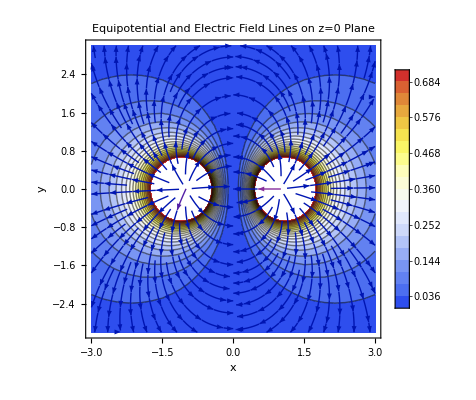

```mathematica
(*定义常数和电荷参数*)k=1;q=1;
q1=q;pos1={1,0,0};
q2=q;pos2={-1,0,0};
q3=-2 q;pos3={0,0,1};

(*定义两点间距离函数*)
dist[p_]:=Sqrt[(x-p[[1]])^2+(y-p[[2]])^2+(z-p[[3]])^2];

(*1. 写出总电势 phi (标量叠加原理)*)
potential=k*(q1/dist[pos1]+q2/dist[pos2]+q3/dist[pos3]);
Print["Potential phi(x,y,z) constructed."]

(*2. 计算电场 E=-Grad phi*)
Efield=-Grad[potential,{x,y,z}];
Print["E-field calculated."]

(*准备绘图：将 z=0 代入*)
phiZ0=potential/. z->0;
ExyZ0=Efield[[1;;2]]/. z->0;(*取 E 的 x,y 分量用于 StreamPlot*)(*---修正部分开始---*)(*3. 绘制等势线 (ContourPlot)-去掉单独的标题*)plotContour=ContourPlot[phiZ0,{x,-3,3},{y,-3,3},Contours->20,PlotLegends->Automatic,ColorFunction->"TemperatureMap"];

(*4. 绘制电场线 (StreamPlot)-去掉单独的标题*)
plotStream=StreamPlot[ExyZ0,{x,-3,3},{y,-3,3},StreamStyle->Orange];

(*5. 显示叠加图，并在这里统一添加标题*)
Show[plotContour,plotStream,PlotLabel->"Equipotential and Electric Field Lines on z=0 Plane",PlotRange->All,(*确保所有元素都显示出来*)FrameLabel->{"x","y"}]
```

```mathematica
(*1. 寻找 E=0 的点*)(*根据对称性，平衡点很可能在 z 轴上 (x=0,y=0)*)(*我们先尝试在 z 轴上寻找解*)EzOnAxis=Efield[[3]]/. {x->0,y->0};
(*求解 z 轴上的零点*)
zSol=NSolve[EzOnAxis==0&&z<2&&z>-2,z];
Print["Potential Equilibrium points on Z-axis: ",zSol]

(*验证完整矢量场是否为0*)
eqPoints={0,0,z}/. zSol;
EatPoints=(Efield/. {x->0,y->0,z->#})&/@(z/. zSol);
Print["E-field at these points: ",EatPoints]

(*2. 在图中标记这些点*)
Show[VectorPlot3D[Efield,{x,-2,2},{y,-2,2},{z,-2,2},RegionFunction->Function[{x,y,z,vx,vy,vz},Norm[{x,y,z}]>0.5],VectorPoints->10],Graphics3D[{Red,PointSize[0.05],Point[eqPoints]}],PlotLabel->"Equilibrium Points in 3D"]

(*3. 稳定性讨论：计算海森矩阵 (Hessian Matrix)*)
(*势能的二阶导数矩阵，或者电场的雅可比矩阵*)
hessianPhi=D[potential,{{x,y,z},2}];

(*定义检查稳定性的函数：查看特征值*)
checkStability[pt_]:=Module[{evals},evals=Eigenvalues[hessianPhi/. {x->pt[[1]],y->pt[[2]],z->pt[[3]]}];
Print["Point: ",pt];
Print["Eigenvalues of Hessian(phi): ",evals];
If[AllTrue[evals,#>0&],Print["Result: Stable Minimum (Impossible in vacuum)"],If[AllTrue[evals,#<0&],Print["Result: Unstable Maximum"],Print["Result: Saddle Point (Unstable)"]]]]

(*对找到的每个点进行分析*)
Map[checkStability,eqPoints];
```

Potential Equilibrium points on Z-axis: {{z→-0.620721}}

E-field at these points: {{0.,0.,0.}}

-Graphics3D-

Point: {0,0,-0.620721}

Eigenvalues of Hessian(phi): {1.89957,-1.14272,-0.756847}

Result: Saddle Point (Unstable)